```mathematica
Ωb=0.045;
Ωcdm=0.226;
Ωm=Ωcdm+Ωb;
ΩΛ=1.-Ωm;
H0rc=0.5;
h=0.703;
H0=100 h; (*km/s/Mpc*)
H[a_]:=H0 a √(Ωm a^-3+ΩΛ);
(*δm=10^-5;*)
β[a_]:=1+4/(3 a) H[a]/H[1] H0rc (1+(a H[a] H'[a])/(2H[a] H[a]));
epsilon[a_,δm_]:=(8 H0rc^2)/(9 β[a]^2)Ωm a^-3 δm;
screening[a_,δm_] = (√(1+epsilon[a,δm])-1)/epsilon[a,δm];
ΔGoverG[a_,δm_]:=2/(3 β[a])(√(1+epsilon[a,δm])-1)/epsilon[a,δm];
```

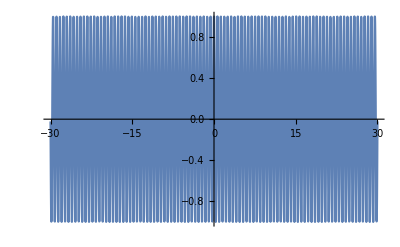

```mathematica
δ[x_]:=Cos[10x]
Plot[δ[x],{x,-30,30}]
```

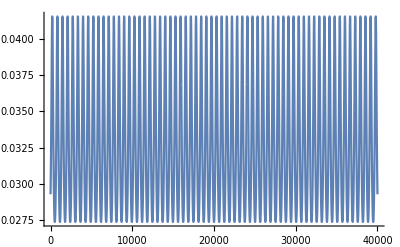

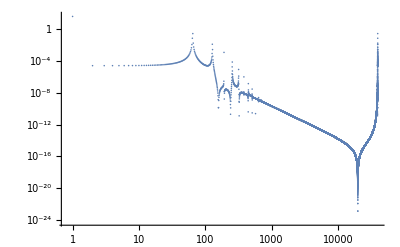

```mathematica
data=Table[ΔGoverG[1./(1+10),δ[r]],{r,-20,20,10^-3}];
Fourier[data];

ListLinePlot[data]
ListLogLogPlot[Abs[Fourier[data]]^2,PlotRange->All]
```